# QR faktorizacija centrosimetricnih matrica

## Konrad Burnik

Za zadanu centrosimetricnu matricu A, trazimo njezinu faktorizaciju oblika A=QR, pri cemu je Q perplekticka realna, tj. Q^t Rn Q = Rn, a R ima oblik dvostrukog konusa.

Primjer za n paran  tj.  n = 2m: 
R=(× | × | × | × | × | ×
  | × | × | × | × |  
  |   | × | × |   |  
  |   | × | × |   |  
  | × | × | × | × |  
× | × | × | × | × | ×) 
Za n neparan tj. n=2m+1:
R=(× | × | × | × | × | × | ×
  | × | × | × | × | × |  
  |   | × | × | × |   |  
  |   |   | × |   |   |  
  |   | × | × | × |   |  
  | × | × | × | × | × |  
× | × | × | × | × | × | ×)

### Implementacija algoritma

```mathematica
CentrosymmetricQRDecomposition[A_]:= 
Module[{x,y,n,At,G,Q,X,Y, k,α1,α2,t},
PNorm[x_]:=Dot[x, Reverse[IdentityMatrix[Length[x]]].x];

BlockGref[X_,Y_]:=N[IdentityMatrix[Dimensions[X][[1]]]-2*(Y-X).PseudoInverse[Transpose[(Y-X)].Reverse[IdentityMatrix[Dimensions[X][[1]]]].(Y-X)].Transpose[(Y-X)].Reverse[IdentityMatrix[Dimensions[X][[1]]]]];

EmbedMatrix[M_,n_]:=Module[{m},
m=Dimensions[M][[1]];
H=IdentityMatrix[n];
H[[(n-m)/2+1 ;;(n-m)/2+m,(n-m)/2+1 ;; (n-m)/2+m]]=M;
Return[H]
];

EmbedMatrix[M_,{n_,m_}]:=Module[{H,p},
H=Table[0, {i,1,n}, {j,1,m}];
p=Dimensions[M][[1]];
H[[1,1;; p]]=M[[1,1;;p]];
H[[n,1;;p]]=M[[m,1;; p]];
Return[H]
];

n=Dimensions[A][[1]];
Q=IdentityMatrix[n];
G=IdentityMatrix[n];
At =A;
For[k=1,k≤ Floor[n/2], k++,
X=At[[k;;n-k+1,k;;n-k+1;;n-2*k+1]];

x=Norm[Transpose[X][[1]]]; y=PNorm[Transpose[X][[1]]];
If[y≠ 0, 
 α1=(√(x^2+√((x^2-y) (x^2+y))))/(√2);α2= (2 (x^2 α1-α1^3))/y;
Y= EmbedMatrix[N[{{α1,α2},{α2,α1}}],{n-2*(k-1),2}];
,(*else*)
Y= EmbedMatrix[{{x,0},{0,x}},{n-2*(k-1),2}];
];
G=EmbedMatrix[BlockGref[X,Y], n];
Q=G.Q;
At = G.At;
];
Return[Chop[{Q,At}]]]
```

### Primjeri:

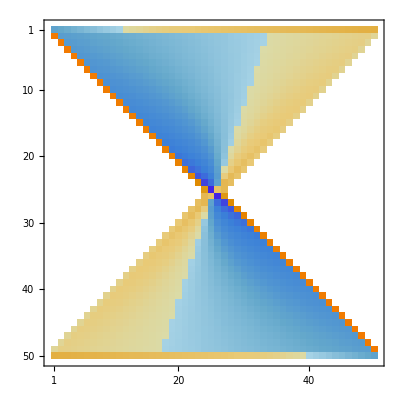
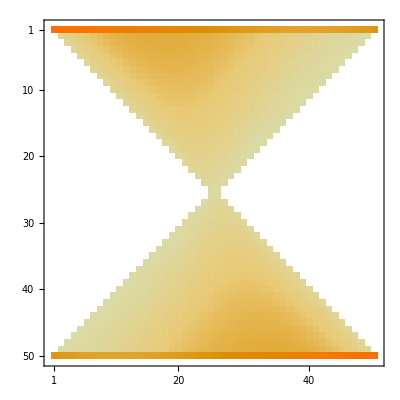

```mathematica
{Q,R}= CentrosymmetricQRDecomposition[ToeplitzMatrix[50]];
 MatrixPlot/@ {Q,R}
```

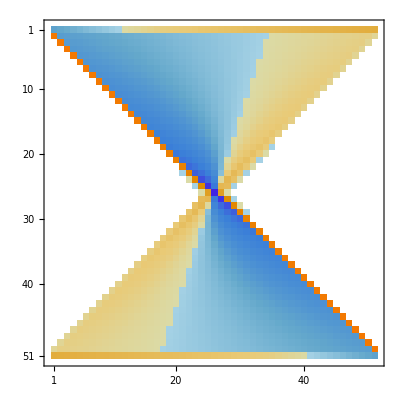
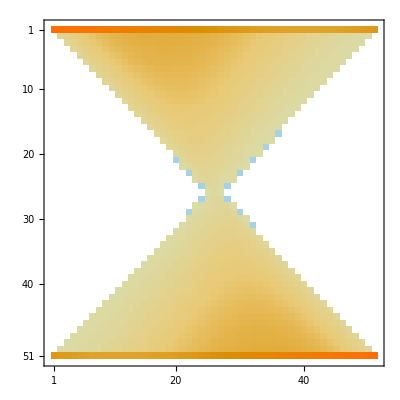

```mathematica
{Q,R}= CentrosymmetricQRDecomposition[ToeplitzMatrix[51]];
 MatrixPlot /@ {Q,R}
```

### Primjena algoritma na rješavanje centrosimetricnih linearnih sustava

```mathematica
SolveTriangleBlock[A_, b_]:=Module[{x,y},
y=Flatten[b];
x=ConstantArray[0,2];
x[[2]]=y[[2]]/A[[2,2]];
x[[1]]=(y[[1]]-A[[1,All]].x) / A[[1,1]];
Return[x];
]
```

```mathematica
SolveBlock[A_,b_]:=Module[{Q,R,x,y},
 {Q,R}=QRDecomposition[A];
  y=Q.b;
x=SolveTriangleBlock[R,y];
Return[x];
]
```

```mathematica
SolveCentrosymmetric[A_,b_]:=Module[{n,m,k,p,q,x,y,z, Q,R},
n=Dimensions[A][[1]];
m=Floor[n/2];
x=ConstantArray[0,n];
{Q,R}= CentrosymmetricQRDecomposition[A];
y=Q.b;  z=Flatten[y];
If[OddQ[n],
x[[m+1]] = z[[m+1]]/ R[[m+1,m+1]];
];
For[k=1, k≤ m, k++,
p=m-k+1;  q=m+k+Boole[OddQ[n]];
{x[[p]], x[[q]]}=
SolveBlock[({{R[[p, p]], R[[p, q]]}, {R[[q, p]], R[[q,q]]}}),({{y[[p]]-R[[p, All]].x}, {y[[q]]-R[[q, All]].x}})];
];
Return[Chop[x]];
]
```

```mathematica
Solve[({{1, 2, 3, 4, 5, 6}, {2, 1, 2, 3, 4, 5}, {3, 2, 1, 2, 3, 4}, {4, 3, 2, 1, 2, 3}, {5, 4, 3, 2, 1, 2}, {6, 5, 4, 3, 2, 1}}).({{x1}, {x2}, {x3}, {x4}, {x5}, {x6}})== ({{1}, {2}, {3}, {0}, {5}, {7}}), {x1,x2,x3,x4,x5,x6}] // N
```

{{x1→1.07143,x2→0.,x3→-2.,x4→4.,x5→-1.5,x6→-0.428571}}

```mathematica
SolveCentrosymmetric[({{1, 2, 3, 4, 5, 6}, {2, 1, 2, 3, 4, 5}, {3, 2, 1, 2, 3, 4}, {4, 3, 2, 1, 2, 3}, {5, 4, 3, 2, 1, 2}, {6, 5, 4, 3, 2, 1}}), ({{1}, {2}, {3}, {0}, {5}, {7}})]
```

{1.07143,0,-2.,4.,-1.5,-0.428571}

```mathematica
Solve[({{1, 2, 3, 4, 5}, {2, 1, 2, 3, 4}, {3, 2, 1, 2, 3}, {4, 3, 2, 1, 2}, {5, 4, 3, 2, 1}}).({{x1}, {x2}, {x3}, {x4}, {x5}})== ({{1}, {-2}, {3}, {4}, {-5}}), {x1,x2,x3,x4,x5}] // N
```

{{x1→-1.83333,x2→4.,x3→-2.,x4→-5.,x5→4.16667}}

```mathematica
SolveCentrosymmetric[({{1, 2, 3, 4, 5}, {2, 1, 2, 3, 4}, {3, 2, 1, 2, 3}, {4, 3, 2, 1, 2}, {5, 4, 3, 2, 1}}),({{1}, {-2}, {3}, {4}, {-5}})]
```

{-1.83333,4.,-2.,-5.,4.16667}